```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<TheDiractionary`
```

```mathematica
dict = RandomSample[Import["CSW21.txt", "List"]];
wordsByLength = GroupBy[dict, StringLength];
```

## Version 1: 7 Letter Scrabble-gorithm

### Run Algorithm

```mathematica
RunVersion1Scrabblegorithm[1]
```

Attempt 1

Bingos Found: {INTORTS}

Tiles Left: 93 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIJKLLLLMMNNNNNOOOOOOOPPQRRRRRSSSTTTTUUUUVVWWXYYZ??

Bingos Found: {INTORTS,ALUMINA}

Tiles Left: 86 AAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIJKLLLMNNNNOOOOOOOPPQRRRRRSSSTTTTUUUVVWWXYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES}

Tiles Left: 79 AAAAAAABBCCDDDEEEEEEEEEEEFFGGGHIIIIIIJKLLLMNNNNOOOOOOPPQRRRRRSSTTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS}

Tiles Left: 72 AAAAAAABBCDDDEEEEEEEEEEEFFGGGIIIIJKLLMNNNNOOOOOOPPQRRRRRSTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER}

Tiles Left: 65 AAAAAAABBCDDEEEEEEEEEEFFGGGIIIIJKLLMNNNNOOOOOQRRRSTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE}

Tiles Left: 58 AAAAAABBDDEEEEEEEEEFFGGGIIILLMNNNNOOOOOQRRRTTTUUUVVWWYYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY}

Tiles Left: 51 AAAAAABBDEEEEEEEEEFFGGGILMNNNNOOOOORRRTTTUUVVWWYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER}

Tiles Left: 44 AAAAAABBDEEEEEEEFFGGLMNNOOOOORRTTTUUVVWWYZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED}

Tiles Left: 37 AAAAAABBEEEEEEFFGGMOOOORRTTTUUVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT}

Tiles Left: 30 AAAABBEEEEEEFFGGOOORRTUVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE}

Tiles Left: 23 AABEEEEEFGOOORRTVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE,BERGERE}

Tiles Left: 16 AAEEFOOOTVVWWZ??

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE,BERGERE,TOWAWAY}

Tiles Left: 9 EEFOOVVZ?

Bingos Found: {INTORTS,ALUMINA,OXHIDES,LITCHIS,DROPPER,JACKSIE,LIQUIDY,ENGINER,NYLONED,AUTOMAT,AUFGABE,BERGERE,TOWAWAY,FOVEOLE}

Tiles Left: 2 VZ

Success!

No Valid Words

```mathematica
dataV1=CloudGet["V.1-WordMaster"];
```

```mathematica
Dataset[dataV1]
```

### Visualize

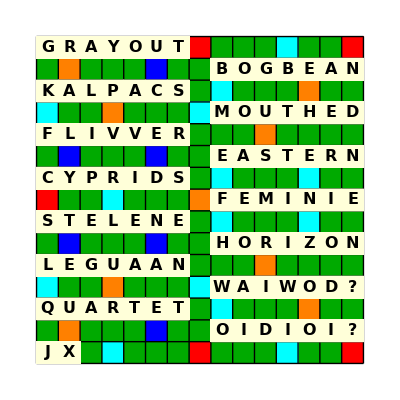

```mathematica
VisualizeVersion1[#]&/@RandomSample[dataV1,1]
```

## Version 2: 8 Letter Scrabble-gorithm

Use 2 blanks on move 14 if none required in move 13?

### Run Algorithm

```mathematica
RunVersion2Scrabblegorithm[1]
```

Bingos: {SUNBURN}

Tiles Left: 93 AAAAAAAAABCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNOOOOOOOOPPQRRRRRSSSTTTTTTUUVVWWXYYZ??

Tiles Used: 7 BNNRSUU

SULPHITE played through: U

Bingos: {SUNBURN,SULPHITE}

Tiles Left: 86 AAAAAAAAABCCDDDDEEEEEEEEEEEFFGGGHIIIIIIIIJKLLLMMNNNNOOOOOOOOPQRRRRRSSTTTTTUUVVWWXYYZ??

Tiles Used: 14 BEHILNNPRSSTUU

RETINUES played through: U

Bingos: {SUNBURN,SULPHITE,RETINUES}

Tiles Left: 79 AAAAAAAAABCCDDDDEEEEEEEEEFFGGGHIIIIIIIJKLLLMMNNNOOOOOOOOPQRRRRSTTTTUUVVWWXYYZ??

Tiles Used: 21 BEEEHIILNNNPRRSSSTTUU

ANATEXES played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES}

Tiles Left: 72 AAAAAAABCCDDDDEEEEEEEFFGGGHIIIIIIIJKLLLMMNNOOOOOOOOPQRRRRTTTTUUVVWWYYZ??

Tiles Used: 28 AABEEEEEHIILNNNNPRRSSSSTTUUX

RIVETTED played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED}

Tiles Left: 65 AAAAAAABCCDDDEEEEEFFGGGHIIIIIIJKLLLMMNNOOOOOOOOPQRRRTTTUUVWWYYZ??

Tiles Used: 35 AABDEEEEEEEHIIILNNNNPRRRSSSSTTTUUVX

JAPINGLY played through: A

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY}

Tiles Left: 58 AAAAAAABCCDDDEEEEEFFGGHIIIIIKLLMMNOOOOOOOOQRRRTTTUUVWWYZ??

Tiles Used: 42 AABDEEEEEEEGHIIIIJLLNNNNNPPRRRSSSSTTTUUVXY

DEBONAIR played through: N

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR}

Tiles Left: 51 AAAAAACCDDEEEEFFGGHIIIIKLLMMNOOOOOOOQRRTTTUUVWWYZ??

Tiles Used: 49 AAABBDDEEEEEEEEGHIIIIIJLLNNNNNOPPRRRRSSSSTTTUUVXY

GRECISED played through: S

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED}

Tiles Left: 44 AAAAAACDEEFFGHIIIKLLMMNOOOOOOOQRTTTUUVWWYZ??

Tiles Used: 56 AAABBCDDDEEEEEEEEEEGGHIIIIIIJLLNNNNNOPPRRRRRSSSSTTTUUVXY

KAUMATUA played through: U

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA}

Tiles Left: 37 AAACDEEFFGHIIILLMNOOOOOOOQRTTUVWWYZ??

Tiles Used: 63 AAAAAABBCDDDEEEEEEEEEEGGHIIIIIIJKLLMNNNNNOPPRRRRRSSSSTTTTUUUVXY

TETANOID played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID}

Tiles Left: 30 AACEFFGHIILLMOOOOOOQRTUVWWYZ??

Tiles Used: 70 AAAAAAABBCDDDDEEEEEEEEEEEGGHIIIIIIIJKLLMNNNNNNOOPPRRRRRSSSSTTTTTUUUVXY

LEGALIST played through: S

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID,LEGALIST}

Tiles Left: 23 ACFFHIMOOOOOOQRUVWWYZ??

Tiles Used: 77 AAAAAAAABBCDDDDEEEEEEEEEEEEGGGHIIIIIIIIJKLLLLMNNNNNNOOPPRRRRRSSSSTTTTTTUUUVXY

VORACITY played through: T

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID,LEGALIST,VORACITY}

Tiles Left: 16 FFHMOOOOOQUWWZ??

Tiles Used: 84 AAAAAAAAABBCCDDDDEEEEEEEEEEEEGGGHIIIIIIIIIJKLLLLMNNNNNNOOOPPRRRRRRSSSSTTTTTTUUUVVXYY

WOODRUFF played through: R with a blank D

Bingos: {SUNBURN,SULPHITE,RETINUES,ANATEXES,RIVETTED,JAPINGLY,DEBONAIR,GRECISED,KAUMATUA,TETANOID,LEGALIST,VORACITY,WOODRUFF}

Tiles Left: 9 HMOOOQWZ?

Tiles Used: 91 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHIIIIIIIIIJKLLLLMNNNNNNOOOOOPPRRRRRRSSSSTTTTTTUUUUVVWXYY?

```mathematica
dataV2=CloudGet["V.2-WordMaster"];
```

```mathematica
Dataset[RandomSample[CloudGet["V.2-WordMaster"],5]]
```

```mathematica
Dataset[dataV2]
```

### Visualize

```mathematica
data=RandomChoice[dataV2]
```

<|Bingos→{TINCHEL,TONETTES,EKISTICS,ANIMATES,WEENIEST,DEVELOPE,HALLOWER,PRANDIAL,OVERNAME,GUARDDOG,BOOBYISH,JANIZARY,FURFUROL,QUADDING},Overlaps→{T,E,I,S,E,H,L,A,D,S,N,R,D},Blanks→{L,N},Tiles Remaining→{I,X}|>

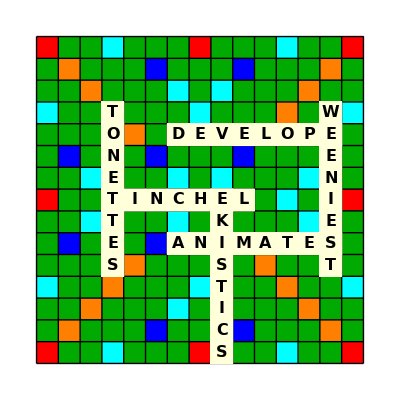

```mathematica
VisualizeVersion2[game_]:=Module[{epilog,board=CreateInitialScrabbleBoard[],bingos=game["Bingos"]},(*Place Bingos on board.*)
epilog=UpdateScrabbleBoard[bingos[[1]],{"H",4},"Right",{}];
epilog=UpdateScrabbleBoard[bingos[[2]],{"D",4},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[3]],{"H",9},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[4]],{"J",7},"Right",epilog];
epilog=UpdateScrabbleBoard[bingos[[5]],{"D",14},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[6]],{"E",7},"Right",epilog];
Show[board,ImageSize->400,Epilog->epilog]
]

VisualizeVersion2[data]
```

## Version 3: Actual Scrabble Game

```mathematica
Do[
board=CreateInitialScrabbleBoard[]; (* Create Graphic of Empty Scrabble Board. *)
assoc=<||>;
remainingCounts=tiles[[All,"Quantity"]]; (* Initial Tiles Remaining. *)
usedCounts=AssociationThread[Keys[tiles],Table[0,27]]; (* Initially Zero Tiles have been used. *)

(* Turn 1. *)
pos=RandomChoice[Table[{"H",col},{col,2,8,1}]]; (* Random Position in Row H. *)
word=Echo@RandomChoice[wordsByLength[7]];
remainingCounts=UpdateRemainingTileCount[remainingCounts,word,0]; (* Update Tiles Remaining. *)

If[remainingCounts===tiles[[All,"Quantity"]], (* Starting 7-letter word must not require blanks. *)
Print[word, ": Choose another Starter"];
Continue[];];

usedCounts=UpdateUsedTileCount[usedCounts,word]; (* Update Tiles Used. *)

AppendTo[assoc,1-><|"Bingo"->word,"Position"->pos,"Direction"->"Right"|>]; (* Append to Master Association, *)
epilogState=UpdateScrabbleBoard[word,pos, "Right",{}]; (* Epilog of Turn 1. *)
Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];

Module[{next=False},(* Initialize flag. *)
Do[
  word=Echo@wordsByLength[8][[i]]; (* Add functionality for checking tiles left. *)
  If[Length[assoc]<12,b=0,b=1];


  overlapTileOptions= Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]];
  If[overlapTileOptions==={},Print[word," Has No Overlaps!"]; next=True];

Map[ (* Check the remaining counts for each overlap option. *)
If[
UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b]==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#] (* Keep only options that do not need unavailable tiles. *)
]&,overlapTileOptions
];
If[overlapTileOptions==={},(*Print["No Valid Plays"];*)next=True];
overlapVectors=Echo@FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
possibleEpilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,overlapVectors];
If[overlapVectors==={},(*Print["Nowhere to Play!"];*) next=True];
  
  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
	{currentBoard=board,localEpilogState,dIdx=idx},
	localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
	Column[{
		Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
		Button[
			"Select",
			AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
			remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],b];
			usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
			epilogState=localEpilogState;
			next=True;(* Flag is set to True when selected *)
			Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
			Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]]
			]
		}]
		],
	{idx,Length[overlapVectors]}],
	{If[overlapTileOptions=!={},Button["Skip",next=True],Nothing]}
	]
	];
	If[next==False,Print[boardOptions]];
WaitUntil[next===True];
	next=False;
   ];
,{i,50}
  ];
],
1
]
```

UNSHOTS

Tiles Left: 93 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHIIIIIIIIIJKLLLLMMNNNNNOOOOOOOPPQRRRRRRSSTTTTTUUUVVWWXYYZ??

Tiles Used: 7 HNOSSTU

VERBINGS

{{{C,4},Down,N},{{A,5},Down,S},{{A,9},Down,S}}

Skip

Tiles Used: 14 BEGHINNORSSTUV

Tiles Left: 86 AAAAAAAAABCCDDDDEEEEEEEEEEEFFGGHIIIIIIIIJKLLLLMMNNNNOOOOOOOPPQRRRRRSSTTTTTUUUVWWXYYZ??

VENOMERS

{{{F,4},Down,N},{{E,7},Down,O},{{A,5},Down,S},{{B,8},Right,E},{{B,4},Right,E},{{F,7},Right,N},{{C,3},Right,R}}

Skip

Tiles Used: 21 BEEGHIMNNNOORRSSSTUVV

Tiles Left: 79 AAAAAAAAABCCDDDDEEEEEEEEEEFFGGHIIIIIIIIJKLLLLMNNNOOOOOOPPQRRRRSTTTTTUUUWWXYYZ??

SALTCATS

{{{H,5},Down,S},{{A,5},Down,S},{{B,15},Down,S}}

Skip

Tiles Used: 28 AABCEEGHILMNNNOORRSSSSTTTUVV

Tiles Left: 72 AAAAAAABCDDDDEEEEEEEEEEFFGGHIIIIIIIIJKLLLMNNNOOOOOOPPQRRRRTTTUUUWWXYYZ??

ADAPTORS

{}

PRIMULAS

{}

WEBBIEST

{}

ZIGANKAS

{}

APPEARER

{{{M,5},Right,A},{{M,1},Right,A}}

Skip

Tiles Used: 35 AAABCEEEEGHILMNNNOOPPRRRRSSSSTTTUVV

Tiles Left: 65 AAAAAABCDDDDEEEEEEEEFFGGHIIIIIIIIJKLLLMNNNOOOOOOQRRTTTUUUWWXYYZ??

DIALYZED

{{{G,7},Down,E},{{E,8},Right,I},{{J,2},Right,L}}

Skip

Tiles Used: 42 AAAABCDDEEEEEGHIILMNNNOOPPRRRRSSSSTTTUVVYZ

Tiles Left: 58 AAAAABCDDEEEEEEEFFGGHIIIIIIIJKLLLMNNNOOOOOOQRRTTTUUUWWXY??

PREDIALS

{}

IMPLORES

{}

CIMINITE

{{{F,7},Down,E},{{G,3},Down,I},{{E,3},Down,I},{{E,8},Right,I},{{E,6},Right,I},{{E,4},Right,I},{{F,5},Right,N}}

Skip

Tiles Used: 49 AAAABCCDDEEEEEEGHIIIIILMMNNNOOPPRRRRSSSSTTTTUVVYZ

Tiles Left: 51 AAAAABDDEEEEEEFFGGHIIIIJKLLLNNNOOOOOOQRRTTUUUWWXY??

SCRUPLED

{}

MOSASAUR

{}

ECHIDNAS

{}

REFLOATS

{}

BUMMOCKS

{}

INDIGENS

{}

ICEWINES

{}

UNSMOOTH

{}

SUCCUBUS

{}

PUGMARKS

{}

NEWSCLIP

{}

SHARKISH

{}

DEVIATES

{}

SYRPHIAN

{}

SMEARING

{}

TERZETTI

{}

OVERCOOL

{}

VIOLABLE

{}

BEDQUILT

{{{H,2},Down,D},{{A,13},Down,E},{{E,12},Down,E},{{E,3},Down,I},{{D,3},Down,U}}

Skip

Tiles Used: 56 AAAABBCCDDDEEEEEEGHIIIIIILLMMNNNOOPPQRRRRSSSSTTTTTUUVVYZ

Tiles Left: 44 AAAAADEEEEEEFFGGHIIIJKLLNNNOOOOOORRTUUWWXY??

FERMENTS

{}

ACROTISM

{}

REDEEMED

{}

WILLABLE

{}

SPRAGGED

{}

ANTIRAPE

{{{G,2},Down,P},{{G,3},Down,P}}

Skip

DRAGONET

{{{G,7},Down,E},{{D,7},Down,O},{{A,14},Down,R}}

Skip

Tiles Used: 63 AAAAABBCCDDDDEEEEEEEGGHIIIIIILLMMNNNNOOOPPQRRRRSSSSTTTTTTUUVVYZ

Tiles Left: 37 AAAAEEEEEFFGHIIIJKLLNNOOOOORRUUWWXY??

EUTHYMIA

{}

MONOTYPE

{}

BORAZONS

{}

CREDENZA

{}

SCRUPLER

{}

SHIPMATE

{}

ORTHOEPY

{}

NASCENCE

{}

ABHORRED

{}

BESCOURS

{}

SCUCHINS

{}

ABUTILON

{}

## Visualize End Result

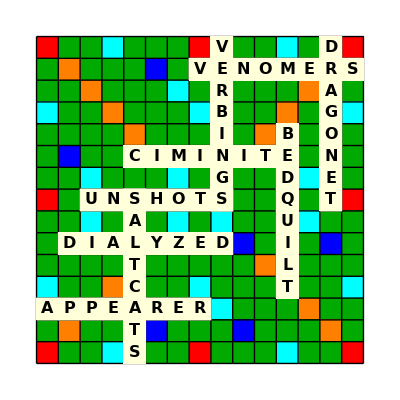

```mathematica
board=CreateInitialScrabbleBoard[];
Show[board,Epilog->epilogState]
```

```mathematica
Dataset[assoc]
```

### Finding Words when Necessary

```mathematica
dict=RandomSample[Import["CSW21.txt","List"]];
wordsByLength=GroupBy[dict,StringLength];
```

```mathematica
Select[wordsByLength[7],First[Characters[#]]=="C"&&Last[Characters[#]]=="G"&]
```

{CYCLING,CHOWING,CUCKING,CHARING,CURDING,CUTTING,CATLING,COMPING,CHIVING,CREWING,CAUMING,CRATING,CURLING,CALVING,CAPPING,CELLING,COONDOG,CANNING,CONNING,CUMMING,CHIMING,CUBBING,CRANNOG,CADGING,CHAWING,CULLING,COINING,CLAYING,CYMLING,CLEPING,CHAFING,CURBING,CARTING,CLIPING,CUFFING,CHIDING,CHINING,CEASING,CRINING,COUPING,COPPING,CEILING,CERNING,CRANING,CODLING,COILING,CHUTING,CABBING,COLTING,CHASING,CASTING,CANTDOG,CENSING,COAMING,CAMPONG,CROWING,CRAPING,COIFING,CARLING,CABLING,COSHING,CLOWING,CAUSING,COOPING,COZYING,CLOKING,COLLING,CONKING,CACHING,CUPPING,COATING,CHEFING,CACKING,CESSING,CURVING,CIELING,CAMMING,CHINWAG,CANTING,CLONING,CODDING,COURING,COSTING,CUSSING,COOKING,CASHING,CATELOG,CATTING,CARKING,COMBING,CLYPING,CATJANG,CALLING,CRIMING,COWKING,COBBING,COALING,CASKING,CORKING,COOMING,CHEWING,CRAZING,CLAWING,CURSING,COFFING,CHACING,CURRING,CONLANG,COAXING,CRAKING,COWLING,CROMING,CALKING,COTTING,CLEWING,CHOKING,CISSING,COPYING,CLOSING,COSYING,CARPING,COCKING,CREPING,CUNNING,CHUSING,CALMING,CAMPING,CEAZING,COGGING,COPSING,CLUEING,CARVING,CHORING,COWPING,CORDING,CULMING,CARDING,CRAVING,CLOYING,CORNING,CATALOG,CREEING,COOLING}

## Prove it is Solvable

```mathematica
blocks=Table[
  StringJoin[Table[" ",If[num==1,7,8]]],
  {num,1,14}
];
BingoIndex[pos_,num_,dir_,epilogState_] :=
Module[{ x=(pos[[2]]-1),y=15-(LetterNumber[pos[[1]]]-1)},
Append[epilogState,Text[Column[{Style[ToString[num],12,Bold],Style[ToString[dir],12,Bold]},Center,0],{x+0.5,y-0.5}]]
]
board=CreateInitialScrabbleBoard[];
```

```mathematica
epilog={};
epilog=UpdateScrabbleBoard[blocks[[1]], {"H",2}, "Right",epilog];
epilog=BingoIndex[{"H",2},1,"→",epilog];
turns[1]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[2]], {"A",3}, "Down",epilog];
epilog=BingoIndex[{"A",3},2,"↓",epilog];
turns[2]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[3]], {"A",5}, "Down",epilog];
epilog=BingoIndex[{"A",5},3,"↓",epilog];
turns[3]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[4]], {"A",8}, "Down",epilog];
epilog=BingoIndex[{"A",8},4,"↓",epilog];
turns[4]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[5]], {"A",7}, "Right",epilog];
epilog=BingoIndex[{"A",7},5,"→",epilog];
turns[5]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[6]], {"C",7}, "Right",epilog];
epilog=BingoIndex[{"C",7},6,"→",epilog];
turns[6]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[7]], {"E",7}, "Right",epilog];
epilog=BingoIndex[{"E",7},7,"→",epilog];
turns[7]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[8]], {"E",10}, "Down",epilog];
epilog=BingoIndex[{"E",10},8,"↓",epilog];
turns[8]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[9]], {"J",8}, "Right",epilog];
epilog=BingoIndex[{"J",8},9,"→",epilog];
turns[9]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[10]], {"H",13}, "Down",epilog];
epilog=BingoIndex[{"H",13},10,"↓",epilog];
turns[10]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[11]], {"H",15}, "Down",epilog];
epilog=BingoIndex[{"H",15},11,"↓",epilog];
turns[11]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[12]], {"H",2}, "Down",epilog];
epilog=BingoIndex[{"I",2},12,"↓",epilog];
turns[12]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[13]], {"H",4}, "Down",epilog];
epilog=BingoIndex[{"H",4},13,"↓",epilog];
turns[13]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[14]], {"N",4}, "Right",epilog];
epilog=BingoIndex[{"N",4},14,"→",epilog];
turns[14]=Show[board,Epilog->epilog];
```

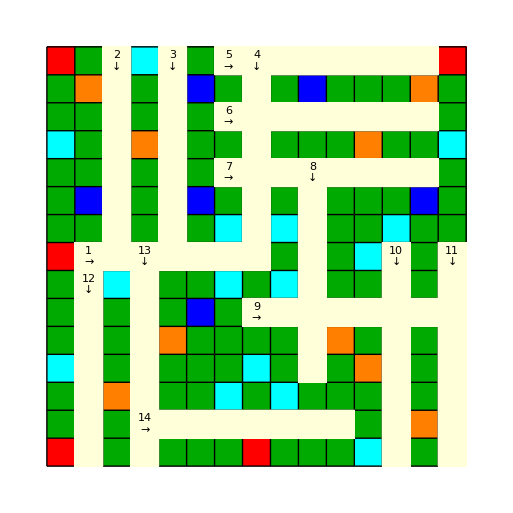

```mathematica
Show[board,Epilog->epilog]
```

```mathematica
Animate[turns[i],{i,1,14,1}]
```

## Testing

```mathematica
DynamicModule[{value=1,i=1,iteration=1,maxIterations=5},
  Dynamic[
    If[iteration<=maxIterations,
      Row[{
        Button["Click Me",
          (value=value*2;
           iteration++;
          )
        ],
        "Iteration: ",iteration, " Value: ",value
      }],
      "All iterations completed"
    ]
  ],
  Initialization:>(value=1;i=1;iteration=1)
]
```